```mathematica
M=100;
lmax=1500;
K[l_]:=N@SparseArray[{{j_,j_}->(j+1/2)^2 1/j^2+Boole[j>1](j-1/2)^2 1/j^2+(l(l+1))/j^2,{i_,j_}/;Abs[j-i]==1->-((i+j)/2)^2/(i j)},{M,M}]
```

```mathematica
ClearAll[k,u]
k[l_]:=k[l]=Eigenvalues@K[l]
u[l_]:=u[l]=Eigenvectors@K[l]
```

```mathematica
u[2]ᵀ.DiagonalMatrix[k[2]].u[2]-K[2]//Chop;
```

```mathematica
(* below we could also use P[l_]=MatrixPower[K[l],1/2]/2 but it would be slower *)
```

```mathematica
ClearAll[P,X]
P[l_]:=P[l]=1/2 u[l]ᵀ.DiagonalMatrix[k[l]^(1/2)].u[l]//Chop[#,10^-20]&
X[l_]:=X[l]=1/2 u[l]ᵀ.DiagonalMatrix[k[l]^(-1/2)].u[l]//Chop[#,10^-20]&
```

```mathematica
PV[l_,n_]:=P[l]_⟦1;;n,1;;n⟧
XV[l_,n_]:=X[l]_⟦1;;n,1;;n⟧
```

```mathematica
cv[l_,n_]:=√Eigenvalues[XV[l,n].PV[l,n]]
```

```mathematica
ClearAll[s]
s[l_,n_]:=s[l,n]=(cv[l,n]+1/2)Log[cv[l,n]+1/2]-(cv[l,n]-1/2)Log[cv[l,n]-1/2]/.Indeterminate->0//Total//Chop
```

```mathematica
tbs=Monitor[Table[{l,(2l+1)s[l,50]},{l,lmax}],l];
```

We can check that npower=3 and nLog=1 do indeed seem best:

```mathematica
Manipulate[
guess=(1+Log[l]^nLog)/l^nPower;
prediction=Table[{1,guess},{l,lmax}];
tbs/prediction//ListPlot,{nLog,{0,1,2,3,4}},{nPower,{1,2,3,4,5}}]
```

```mathematica
tbS=Monitor[Table[{n+1/2,Sum[(2l+1)s[l,n],{l,0,lmax}]},{n,50}],n];
```

```mathematica
fit=c R^2+a Log[R]/.FindFit[tbS,c R^2+a Log[R],{c,a},R]
```

0.293991 R^2+0.140959 Log[R]

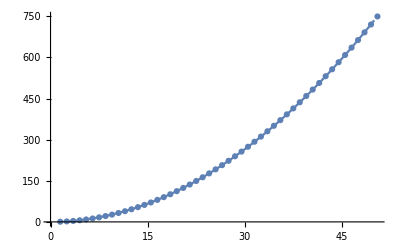

```mathematica
Show[ListPlot[tbS],Plot[fit,{R,2,50}]]
```

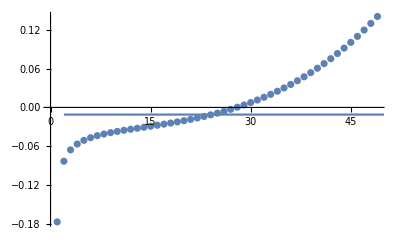

```mathematica
Show[Table[a/.FindFit[tbS⟦1;;nmax⟧,c R^2+a Log[R],{c,a},R],{nmax,2,50}]//ListPlot,Plot[-1/90,{n,2,50}]]
```